This Mathematica notebook solves a non-linear partial differential equation describing a non-evaporating liquid film (with periodic boundary conditions) under the influence of stabilizing surface tension, stabilizing gravity and destabilizing thermocapillarity.

For more details, the reader is referred to: 
“Nonlinear dynamics of three-dimensional long-wave Marangoni instability in thin liquid films” (http://pof.aip.org/resource/1/phfle6/v12/i7/p1633_s1)

“Spontaneous rupture of thin liquid films due to thermocapillarity: A full-scale direct numerical simulation ” (http://pof.aip.org/resource/1/phfle6/v7/i9/p2291_s1)

Aneet D Narendranath © 2013

```mathematica
(*Needs["VectorAnalysis`"]
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];*)
{xMin,xMax}={-π/0.0677,π/0.0677}; (*Domain size*)
k=0.0677; (*Perturbation Wavenumber*)
TMax=2000; (*Maximum time (non-dimensional)*)
(*uSol[t_,x_]=u[t,x]/.*)uSolpbc[t_,x_]=u[t,x]/.NDSolve[{D[u[t,x], t]==-100 D[(u[t,x]^3 D[u[t,x], x,x,x]), x]+1/3 D[(u[t,x]^3 D[u[t,x], x]), x]-5 D[((u[t,x]/(1+u[t,x]))^2 D[u[t,x], x]), x],u[0,x]==1-0.1 Cos[k*x],
u[t,xMin]== u[t,xMax],
Derivative[0,1]u[t,xMin]==Derivative[0,1]u[t,xMax],
Derivative[0,2]u[t,xMin]==Derivative[0,2]u[t,xMax],
Derivative[0,3]u[t,xMin]==Derivative[0,3]u[t,xMax]},
u,
{t,0,TMax},
{x,xMin,xMax},
(*PrecisionGoal->Automatic,*)
MaxSteps->100000,Method->{"MethodOfLines","Method"->"BDF","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->200,"DifferenceOrder"->5}}]⟦1⟧
```

NDSolve::ndsz: At t == 1712.35, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 12949.3 at t = 1712.35 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 200 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[{{0.,1712.35},{-46.4046,46.4046}},<>][t,x]

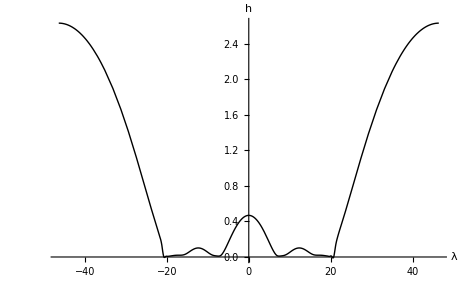

```mathematica
Plot[
uSolpbc[1744,x],{x,xMin,xMax},PlotStyle->{Black,Thick},
AxesLabel->{"λ","h"},
BaseStyle->{FontWeight->"Plain",FontSize->18}
]
```

```mathematica
p1=Plot[uSolpbc[0.1 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p2=Plot[uSolpbc[0.5 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p3=Plot[uSolpbc[0.8 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p4=Plot[uSolpbc[ TMax,x],{x,xMin,xMax},PlotStyle->Blue];
Show[p1,p2,p3, PlotRange->All,FrameLabel->{"x=λ","h(x,t)"},PlotLabel->"G=1,S=100,Pr=7.02,M=35.1,K=1,B=0",Frame->True,TextStyle->{FontFamily->"Helvetica",FontSize->12}]
```

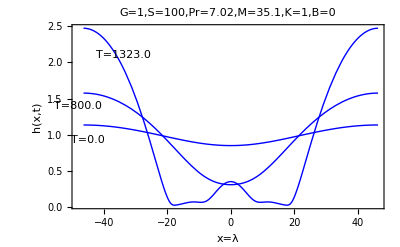

```mathematica
NIntegrate[uSolpbc[0.1 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[0.5 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[0.8 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[ TMax,x],{x,xMin,xMax}]
```

92.8092

92.8079

92.808

92.8076

```mathematica
Manipulate[
Plot[uSolpbc[t,x], {x,xMin,xMax}, PlotRange->{{xMin,xMax},{0,2}},PlotStyle->Red],
{t,0,TMax,TMax/25}]
```